# Mattis-Bardeen theory

## frequency dependent complex normalized optical conductivity for superconductors

-Graphics--Graphics-
From, Martin Dressel, George Grüner-Electrodynamics of solids_ optical properties of electrons in matter-Cambridge University Press (2002)

-Prashant Chauhan

Sept 29th, 2017

Notes : The  parameters and constants are as follows: T = temperature, w = frequency (f), e = energy, d = Δ(T), d0 = Δ(0), suitable units would be milli electron volts ., Sigma1s and sigma2s are real and img part of complex conductivity. We write planck constant h = 4.135667662/10^12 meV.s x  10^12 to convert it to THz units; so w will be in THz. You can assign data folder for data transfer at the bottom of the page.

Constants:

```mathematica
k=8.6173303/10^2;d0=0.33;Tc=2.3;(*h=4.135667662/10^12 meV.s*) h= 4.135667662;T=0.01;
```

functions:

```mathematica
d[T_]:=d0*Tanh[1.74*√(Tc/T-1)](*(approximate form of superconducting gap)*)
```

```mathematica
(*d[T1_]:=Quiet[(2 d1 d0)/1.76/.FindRoot[NIntegrate[Tanh[(√(x^2+d1^2))/T1]/(√(x^2+d1^2)),{x,0,12.3611}]==1/0.3,{d1,1}]];*) (*Exact form for superconducting gap*)
```

```mathematica
f[m_]:=1/(ⅇ^(m/(k T))+1)
K[w_,e_]:=Abs[e^2+h w e+d[T]^2]/(√((e+h w)^2-d[T]^2))
A[w_,e_]:=((f[e]-f[e+h w]) K[w,e])/(√(e^2-d[T]^2))
B[w_,e_]:=((1-2 f[e+h w]) K[w,e])/(√(e^2-d[T]^2))
B2[w_,e_]:=((1-2 f[e+h w]) K[w,e])/(√(d[T]^2-e^2))
intA[w_]:=NIntegrate[A[w,e],{e,d[T],1000 d[T]},Method->{"GaussKronrodRule","GaussPoints"->15},MaxRecursion->18,WorkingPrecision->13]
intB[w_]:=Piecewise[{{0,h w<2 d[T]},{NIntegrate[B[w,e],{e,d[T]-h w,-d[T]},Method->{"GaussKronrodRule","GaussPoints"->12},MaxRecursion->18,WorkingPrecision->10],h w≥2 d[T]}}]
sigma1s[w_]:=(2 intA[w]+intB[w])/(h w)
sigma2s[w_]:=Piecewise[{{NIntegrate[B2[w,e]/(h w),{e,d[T]-h w,d[T]},Method->{"GaussKronrodRule","GaussPoints"->15},MaxRecursion->18,WorkingPrecision->13],h w≤2 d[T]},{NIntegrate[B2[w,e]/(h w),{e,-d[T],d[T]},Method->{"GaussKronrodRule","GaussPoints"->15},MaxRecursion->18,WorkingPrecision->13],h w>2 d[T]}}]
```

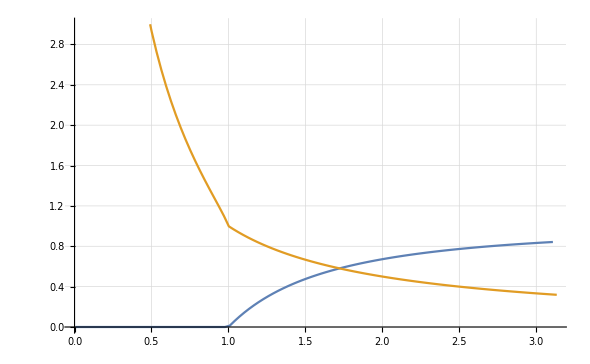

```mathematica
data=Table[{h*w/(2*d[T]),sigma1s[w]},{w,0.001,0.5,0.005}] ;(*ListPlot[{data},PlotRange->All,Joined->True]*)
data1=Table[{h*w/(2*d[T]),sigma2s[w]},{w,0.01,0.5,0.005}] ;ListPlot[{data,data1},PlotRange->{{0,3}}, Joined->True, GridLines-> Automatic, GridLinesStyle->Directive[Gray, Dashed]]
(*data = Prepend[data, {X,Y}];*)
(*Export["sigma1s.dat",data];Export["sigma2s.dat",data1];*)
```

Setting directory for exporting/import data.

```mathematica
SetDirectory["C:\\Users\\"]
```